## Chromatin looping + PIC recruitment model

## Define transition rate matrix

```mathematica
ass = {km2>0, km1 ≥ 0, kp1>0,kp2>0,kon2 > 0, kon1 ≥ kon2,koff1>0,koff2>0};
```

Assumptions: (1) productive transcription possible whenever PIC assembled at promoter AND Pol II cluster is present (state  4)
		         (2) rate of PIC assembly is sensitive to local TF concentration (which is itself linearly proportional to nuclear concentration)

```mathematica
Clear["Global`*"]
```

```mathematica
Qact = {{-km1-c*kon1,              kp1,                              0,                          koff2},
               {km1,                   -kp1-c*kon2,                koff1,                           0},
               {0,                               c*kon2,              -koff1-kp2,              km2},
               {c*kon1,                           0,                    kp2,              -koff2-km2}};
```

```mathematica
MatrixForm[Qact]
```

(-km1-c kon1 | kp1 | 0 | koff2
km1 | -c kon2-kp1 | koff1 | 0
0 | c kon2 | -koff1-kp2 | km2
c kon1 | 0 | kp2 | -km2-koff2)

```mathematica
Total[Qact]
```

{0,0,0,0}

```mathematica
Qact = Qact /. km2 ->1-koff2;
```

## Calculate gradient wrt c

```mathematica
eigVectors = Eigenvectors[Qact];
```

```mathematica
ssRaw = FullSimplify[eigVectors[[1]] / Total[eigVectors[[1]]]]
```

{(koff1 kp1+koff2 (c kon2+kp1) kp2)/(c^2 kon1 kon2 (1-koff2+kp2)+kp1 (koff1+koff2 kp2)+km1 (koff1+koff2 kp2+c kon2 (1+kp2))+c (koff1 kon1 (1-koff2+kp1)+koff2 kon2 kp2+kon1 kp1 (1-koff2+kp2))),(c koff1 (-1+koff2) kon1-km1 (koff1+koff2 kp2))/(c^2 kon1 kon2 (-1+koff2-kp2)-kp1 (koff1+koff2 kp2)+c (koff1 kon1 (-1+koff2-kp1)+kon1 kp1 (-1+koff2-kp2)-koff2 kon2 kp2)-km1 (koff1+koff2 kp2+c kon2 (1+kp2))),(c (-km1 kon2+(-1+koff2) kon1 (c kon2+kp1)))/(c^2 kon1 kon2 (-1+koff2-kp2)-kp1 (koff1+koff2 kp2)+c (koff1 kon1 (-1+koff2-kp1)+kon1 kp1 (-1+koff2-kp2)-koff2 kon2 kp2)-km1 (koff1+koff2 kp2+c kon2 (1+kp2))),(c (km1 kon2 kp2+c kon1 kon2 kp2+kon1 kp1 (koff1+kp2)))/(c^2 kon1 kon2 (1-koff2+kp2)+kp1 (koff1+koff2 kp2)+km1 (koff1+koff2 kp2+c kon2 (1+kp2))+c (koff1 kon1 (1-koff2+kp1)+koff2 kon2 kp2+kon1 kp1 (1-koff2+kp2)))}

Impose constraint that km2 = 1-koff2

```mathematica
pdRate = FullSimplify[ssRaw[[4]]+ ssRaw[[3]]]
```

(c (c kon1 kon2 (-1+koff2-kp2)-km1 kon2 (1+kp2)-kon1 kp1 (1+koff1-koff2+kp2)))/(c^2 kon1 kon2 (-1+koff2-kp2)-kp1 (koff1+koff2 kp2)+c (koff1 kon1 (-1+koff2-kp1)+kon1 kp1 (-1+koff2-kp2)-koff2 kon2 kp2)-km1 (koff1+koff2 kp2+c kon2 (1+kp2)))

#### Calculate derivative wrt c (sharpness)

```mathematica
drdc = FullSimplify[D[pdRate,c] /. {c->1}]
```

(km1^2 kon2 (1+kp2) (koff1+koff2 kp2)+km1 (koff1+koff2 kp2) (kon2 kp1 (1+kp2)+2 kon1 kon2 (1-koff2+kp2)+kon1 kp1 (1+koff1-koff2+kp2))+kon1 (koff1^2 kp1^2+koff1 (-1+koff2) kon1 kon2 (-1+koff2-kp2)-koff2 (kon2+kp1)^2 (-1+koff2-kp2) kp2+koff1 kp1 (2 kon2 (1-koff2+kp2)+kp1 (1+koff2 (-1+kp2)+kp2))))/(koff1 (kon1-koff2 kon1+kp1+kon1 kp1)+(kon2+kp1) (kon1-koff2 kon1+koff2 kp2+kon1 kp2)+km1 (koff1+kon2+(koff2+kon2) kp2))^2

## Take limits where one kind of transition >> the other

#### Rapid PIC assembly/dissasembly

```mathematica
pdRatePIC = kon1*c / (kon1*c + koff2) * kp / (kp + km)
```

(c kon1 kp)/((koff2+c kon1) (km+kp))

```mathematica
drdcPIC = FullSimplify[D[pdRatePIC,c]] /.c->1
```

(koff2 kon1 kp)/((koff2+kon1)^2 (km+kp))

```mathematica
NMaximize[{drdcPIC,koff2>100,kon1>100,km<1,km>0,kp<1,kp>0},{kon1,koff2,kp,km}]
```

{0.25,{kon1→100.244,koff2→100.238,kp→1.0904×10^-7,km→0.}}

#### Rapid Looping/unlooping

```mathematica
pdRateLooping = kon*c / (kon*c + koff) * kp / (kp+km);
```

```mathematica
drdcLooping= FullSimplify[D[pdRateLooping,c]] /.c->1
```

(koff kon kp)/((koff+kon)^2 (km+kp))

```mathematica
NMaximize[{drdcLooping,koff<1,kon>1,km>100,kp>100,kon>0,koff>0},{kon,koff,kp,km}]
```

{0.249953,{kon→1.00189,koff→0.997891,kp→550368.,km→101.461}}

#### Calculate Effective On Rate

Effective on rate

```mathematica
TonEff = FullSimplify[1/pdRate - 1]
```

(-c^2 (-1+koff2) kon1 kon2-c (-1+koff2) kon1 (koff1+kp1)+c koff2 kon2 kp2+kp1 (koff1+koff2 kp2)+km1 (koff1+c kon2+koff2 kp2))/(c (km1 kon2 kp2+c kon1 kon2 kp2+kon1 kp1 (koff1+kp2)))

Switch times btw high and low concentration groups

```mathematica
eq1 = ET1 == -1/Qact[[1,1]] + ET4 *kon1 /-Qact[[1,1]];
```

```mathematica
eq2 = ET4 == -1/Qact[[4,4]] + ET1 *koff2 /-Qact[[4,4]];
```

```mathematica
sol1 = Solve[{eq1,eq2},{ET1,ET4}];
```

```mathematica
Hoff1 = ET1 /. sol1[[1]]
```

-(-1-kon1)/(km1+c kon1-koff2 kon1)

```mathematica
Hoff2 = ET4 /. sol1[[1]]
```

-(km1+koff2+c kon1)/(-km1-c kon1+koff2 kon1)

```mathematica
highProb = ssRaw[[1]] + ssRaw[[4]] /.c->1;
```

```mathematica
RateToLow = FullSimplify[highProb / (Hoff1*ssRaw[[1]]+Hoff2*ssRaw[[4]]) /. c->1 ]
```

((km1+kon1-koff2 kon1) (koff1 (1+kon1) kp1+km1 kon2 kp2+(koff2+kon1) (kon2+kp1) kp2))/(koff1 (1+kon1 (1+km1+koff2+kon1)) kp1+(km1^2 kon2+km1 koff2 kon2+(koff2+2 koff2 kon1+kon1^2) (kon2+kp1)+km1 kon1 (2 kon2+kp1)) kp2)

```mathematica
RateToHigheq = highProb == RateToHigh / (RateToHigh + RateToLow);
```

```mathematica
RateToHighSol =  Solve[RateToHigheq,RateToHigh];
RateToHigh = FullSimplify[RateToHigh /. RateToHighSol[[1]]]
```

((km1+kon1-koff2 kon1) (koff1 (1+kon1) kp1+km1 kon2 kp2+(koff2+kon1) (kon2+kp1) kp2)^2)/((koff1 (1+kon1 (1+km1+koff2+kon1)) kp1+(km1^2 kon2+km1 koff2 kon2+(koff2+2 koff2 kon1+kon1^2) (kon2+kp1)+km1 kon1 (2 kon2+kp1)) kp2) (-(-1+koff2) kon1 (koff1+kon2+kp1)+km1 (koff1+kon2+koff2 kp2)))

#### Switch Rates btw “bound” and “unbound” groups

```mathematica
Beq1 = ET1 == -1/Qact[[1,1]] + ET2 *km1 /-Qact[[1,1]];
```

```mathematica
Beq2 = ET2 == -1/Qact[[2,2]] + ET1 *kp1 /-Qact[[2,2]];
```

```mathematica
Bsol1 = Solve[{Beq1,Beq2},{ET1,ET2}];
```

```mathematica
Uoff1 = ET1 /. Bsol1[[1]]
```

-(-km1-c kon2-kp1)/(c (km1 kon2+c kon1 kon2+kon1 kp1))

```mathematica
Uoff2 = ET2 /. Bsol1[[1]]
```

-(-km1-c kon1-kp1)/(c (km1 kon2+c kon1 kon2+kon1 kp1))

```mathematica
UnboundProb = ssRaw[[1]] + ssRaw[[2]] /.c->1;
```

```mathematica
RateToBound = FullSimplify[UnboundProb / (Uoff1*ssRaw[[1]]+Uoff2*ssRaw[[2]]) /. c->1 ]
```

((km1 kon2+kon1 (kon2+kp1)) (koff1 (km1+kon1-koff2 kon1+kp1)+koff2 (km1+kon2+kp1) kp2))/(koff1 ((km1+kon1) (km1+kon1-koff2 kon1)+(2 km1+kon1-koff2 kon1+kon2) kp1+kp1^2)+koff2 (km1^2+(kon2+kp1)^2+km1 (kon1+kon2+2 kp1)) kp2)

```mathematica
RateToUnboundEq = UnboundProb == RateToUnbound / (RateToUnbound + RateToBound);
```

```mathematica
RateToUnboundSol =  Solve[RateToUnboundEq,RateToUnbound];
RateToUnbound = FullSimplify[RateToUnbound /. RateToUnboundSol[[1]]]
```

((km1 kon2+kon1 (kon2+kp1)) (koff1 (km1+kon1-koff2 kon1+kp1)+koff2 (km1+kon2+kp1) kp2)^2)/((koff1 ((km1+kon1) (km1+kon1-koff2 kon1)+(2 km1+kon1-koff2 kon1+kon2) kp1+kp1^2)+koff2 (km1^2+(kon2+kp1)^2+km1 (kon1+kon2+2 kp1)) kp2) (km1 kon2 (1+kp2)+kon1 kon2 (1-koff2+kp2)+kon1 kp1 (1+koff1-koff2+kp2)))

### Use numerical optimization to gain insight into drivers of sharpness

```mathematica
maxEx = NMaximize[{drdc ,km1 >0, kp1>1,kp2 >0,kp2<1,kon2 > 0, kon1 <100,koff1>0,koff2>0,koff2<1},{ km1, kp1,kp2,kon2, kon1,koff1,koff2}]
```

{0.378447,{km1→7.15307×10^-20,kp1→2.09175,kp2→0.456191,kon2→2.21096,kon1→0.0000655587,koff1→0.000196385,koff2→7.15307×10^-20}}

Key parameters: 1. kp1/kp2 (kp1  > kp2),   2.  kon1 >1, km1 > 1,   3. kp1 < 1

```mathematica
pdRate = pdRate /. c->1
```

```mathematica
pdRate /. maxEx[[2]]
```

0.521286

#### Conduct parameter sweeps to identify trends in model performance

```mathematica
ParamVals= Table[{ koff2->  RandomReal[{0,1}],kp1->  RandomReal[{1,100}],kp2->  RandomReal[{.01,1}],kon1->  RandomReal[{1,100}],kon2->  RandomReal[{.01,1}],koff1->  RandomReal[{1,100}],km1->  RandomReal[{.1,10}]},{10000}];
```

```mathematica
SharpSweep = Table[{drdc/.ParamVals[[i]], pdRate/.ParamVals[[i]]}, {i,1,Length[ParamVals]}];
```

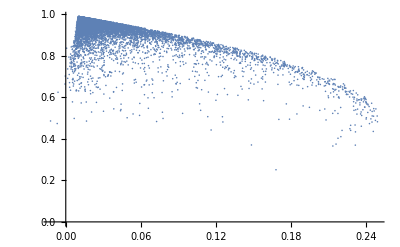

```mathematica
ListPlot[SharpSweep, PlotRange->All]
```

```mathematica
drdc/.ParamVals[[1]]
```

0.0125589

```mathematica
pdRate/.ParamVals[[1]]
```

(c (373413.+82621.5 c))/(3662.88+365990. c+83559.3 c^2+12.6739 (102.959+979.538 c))